## SSH without flux

### number of sites

```mathematica
chainsize=20;
```

### definition of Hamiltonian

```mathematica
s=SparseArray[
{
{i_,i_}->ϵ,
{i_,j_}/;OddQ[i]&&(i-j)==1->Conjugate[ta],
{i_,j_}/;EvenQ[i]&&(i-j)==1->Conjugate[tb],
{i_,j_}/;OddQ[i]&&(j-i)==1->tb,
{i_,j_}/;EvenQ[i]&&(j-i)==1->ta},
{chainsize,chainsize}
]
```

SparseArray[<38>, {20, 20}]

### PBC

```mathematica
s[[1,chainsize]]=Conjugate[ta];
s[[chainsize,1]]=ta;
```

### matrix representation

```mathematica
Normal[s]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5
1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1.
0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

### Diagonalization

```mathematica
ta=.5;tb=1.;ϵ=0;
```

```mathematica
{valores,vectores}=Eigensystem[s];
```

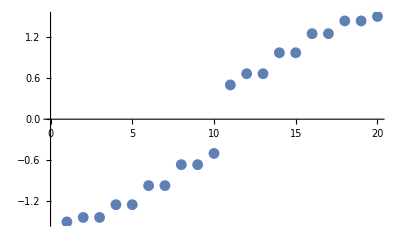

```mathematica
ListPlot[valores//Sort,Joined->False,Mesh->All]
```

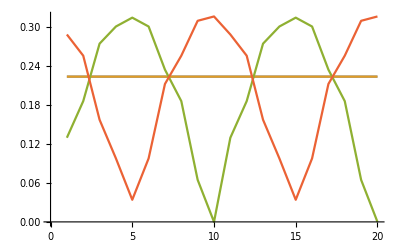

```mathematica
ListPlot[Abs[vectores[[1;;4]]],Joined->True]
```

### test orthogonality

```mathematica
vectores[[1]].vectores[[2]]
```

6.245×10^-17

## with flux

```mathematica
s=SparseArray[
{
{i_,i_}->ϵ,
{i_,j_}/;OddQ[i]&&(i-j)==1->Conjugate[ta],
{i_,j_}/;EvenQ[i]&&(i-j)==1->Conjugate[tb],
{i_,j_}/;OddQ[i]&&(j-i)==1->tb,
{i_,j_}/;EvenQ[i]&&(j-i)==1->ta},
{chainsize,chainsize}
]
```

SparseArray[<38>, {20, 20}]

### Add flux

```mathematica
s[[1,chainsize]]=Conjugate[ta]Exp[-I phi/chainsize];
s[[chainsize,1]]=ta Exp[I phi/chainsize];
```

```mathematica
Normal[s]//MatrixForm
```

(0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 ⅇ^(-(ⅈ phi)/20)
1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0 | 1.
0.5 ⅇ^((ⅈ phi)/20) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0)

```mathematica
Manipulate[{valores,vectores}=Eigensystem[Normal[s]/.phi->phivalue];
Column[{
ListPlot[valores//Sort,Joined->True,Mesh->All],ListPlot[Abs[vectores[[1;;4]]],Joined->True]}],{{phivalue,0},0,3,.001}]
```

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

Set::shape: Lists {valores,vectores} and Eigensystem[s] are not the same shape.

Sort::normal: Nonatomic expression expected at position 1 in Sort[valores].

ListPlot::lpn: Sort[valores] is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 4 in vectores.

ListPlot::lpn: Abs[vectores⟦1;;4⟧] is not a list of numbers or pairs of numbers.

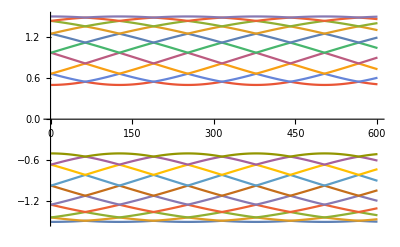

```mathematica
Table[{valores2,vectores2}=Eigensystem[Normal[s]/.phi->phivalue];
Sort[valores2],{phivalue,0,600,1}]//Transpose//ListPlot[#,Joined->True]&
```